# Derivatives vs Differences

-Graphics-

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
D[Sin[x] Exp[-x^2],x]
```

ⅇ^(-x^2) Cos[x]-2 ⅇ^(-x^2) x Sin[x]

```mathematica
f[x_,n_] := x^n
```

```mathematica
D[f[x,n],x]
```

n x^(-1+n)

```mathematica
n x^(-1+n)
```

n x^(-1+n)

```mathematica
DerSin[x_] =  D[Sin[x],x]
```

Cos[x]

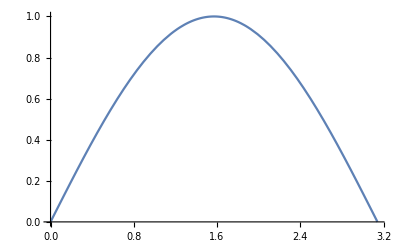

```mathematica
Plot[Sin[x],{x,0,Pi}]
```

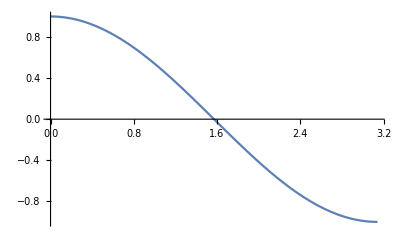

```mathematica
Plot[DerSin[x],{x,0,Pi}]
```

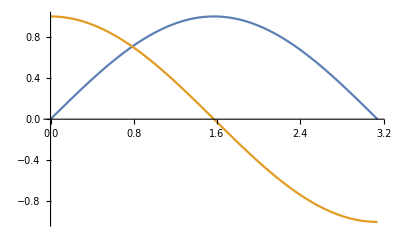

```mathematica
Plot[{Sin[x],DerSin[x]},{x,0,Pi}]
```

```mathematica
diffSin[x_, h_] := (Sin[x+h] - Sin[x])/h
```

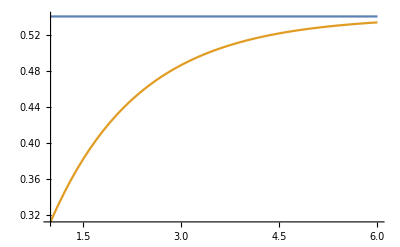

```mathematica
Plot[{DerSin[1],diffSin[1, 2^{-p}]},{p,1,6}]
```

```mathematica
Pi//N
```

3.14159

```mathematica
NumberForm[N[Pi,100]]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
Factorial[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
Delta[fn_,x_, h_] := Module[{func = fn},
(fn[x+h] - fn[x])/h
]
```

```mathematica
Delta[Sin,h]
```

```mathematica
Pochammer[x+1,4] - Pochammer[x,n] - n Pochammer[x,n-1]
```

-n Pochammer[x,-1+n]-Pochammer[x,n]+Pochammer[1+x,4]

```mathematica
Delta[#^4 &,x,h]
```

(-x^4+(h+x)^4)/h

```mathematica
Delta[#^n &,x,1]
```

-x^n+(1+x)^n

```mathematica
Delta[Pochhammer[#-3,4] &,x,1]
```

-(-3+x) (-2+x) (-1+x) x+(-2+x) (-1+x) x (1+x)

```mathematica
Simplify[-(-3+x) (-2+x) (-1+x) x+(-2+x) (-1+x) x (1+x)]
```

4 x (2-3 x+x^2)

```mathematica
Pochhammer[x-2,3]
```

(-2+x) (-1+x) x

```mathematica
Expand[(-2+x) (-1+x) x]
```

2 x-3 x^2+x^3